-Graphics3D-

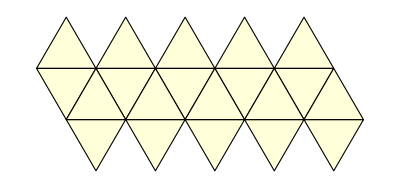

{{1,14},{1,15},{1,16},{2,5},{2,6},{2,13},{3,7},{3,14},{3,19},{4,8},{4,15},{4,20},{5,11},{5,19},{6,12},{6,20},{7,11},{7,16},{8,12},{8,16},{9,10},{9,14},{9,17},{10,15},{10,18},{11,12},{13,17},{13,18},{17,19},{18,20}}

-Graphics3D-

```mathematica
(* use icosahedron function*)
Graphics3D[Dodecahedron[], Boxed->False]
PolyhedronData["Icosahedron", "Net"]
vertices=PolyhedronData["Dodecahedron","VertexCoordinates"];
edges = PolyhedronData["Dodecahedron", "EdgeIndices"]
faces = PolyhedronData["Dodecahedron", "FaceIndices"];Graphics3D[{PolyhedronData["Dodecahedron","Faces"],Table[Text[Style[i,Bold,16],vertices[[i]]],{i,Length[vertices]}]},Boxed->False]
```